### Attempt 1

```mathematica
Module[{gk2r2,embedding},
gk2r2=WeaklyConnectedGraphComponents[
Import[CloudObject[["https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c"](https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c)]],
AspectRatio->2/3][[1]];
SeedRandom[12345];
embedding=Map[#+RandomReal[20,2]&,
GraphEmbedding[gk2r2]];
g = Graph[gk2r2,EdgeStyle->Directive[Hue[0.6,0.4,0.5,.6],Opacity[.15]],
VertexStyle->GrayLevel[.3],VertexCoordinates->embedding];
]
```

```mathematica
peaks = Select[VertexList[g],VertexOutDegree[g,#]==0&];
```

```mathematica
Length[peaks]
```

983

```mathematica
VertexCount[g]
```

2409

```mathematica
peaks[[;;3]]
```

{{{7637860,2147483647}},{{110270820,2147483647}},{{110672164,2145255423}}}

```mathematica
peaks[[;;3]]
```

{{{7637860,2147483647}},{{110270820,2147483647}},{{110672164,2145255423}}}

```mathematica
ArrayPlot[CellularAutomaton[{#[[1, 1]], 2, 2}, {{1}, 0}, 50]]&/@ peaks[[;;3]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListStepPlot[Sort[lts = ParallelMap[{{"[◼]", "TestLifetime"}}[ #[[1, 1]]]&,peaks]]
```

```mathematica
64^3
```

262144

```mathematica
4^9
```

262144

```mathematica
ByteCount[g]
```

1922500

```mathematica
5^7
```

78125

```mathematica
5^3
```

125

```mathematica
5^5
```

3125

```mathematica
evos[[1, 1]]
```

{1949645695365061666240880279649438756218425052453911896507423604934982472152974405994415,5,1}

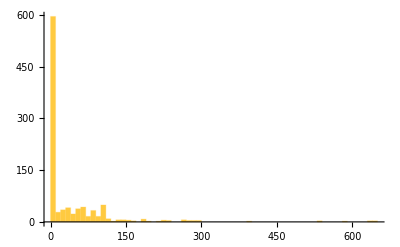

```mathematica
Histogram[ParallelTable[SeedRandom[334222 +i];{{"[◼]", "TestLifetime"}}[{{"[◼]", "RandomRuleMutation"}}[evos[[1, 1]],1,"Symmetric"->True], 1000], {i, 1000}]/.-Infinity->0, {10}, PlotRange->All]
```

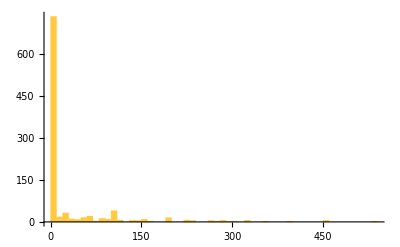

```mathematica
Histogram[ParallelTable[SeedRandom[334222 +i];{{"[◼]", "TestLifetime"}}[{{"[◼]", "RandomRuleMutation"}}[evos[[1, 1]],1], 1000], {i, 1000}]/.-Infinity->0, {10}, PlotRange->All]
```

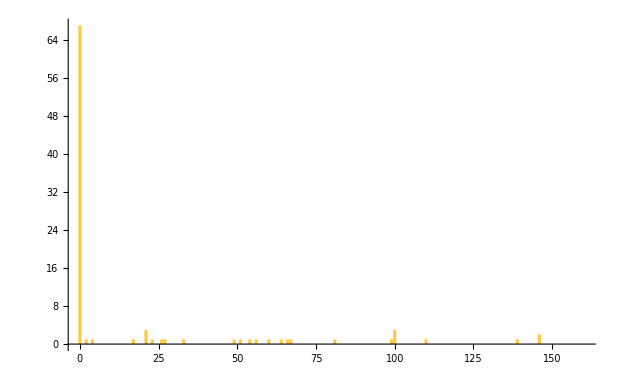

```mathematica
Histogram[Table[SeedRandom[333222 +i];{{"[◼]", "TestLifetime"}}[{{"[◼]", "RandomRuleMutation"}}[evos[[1, 1]],1], 400], {i, 100}]/.-Infinity->0, {1}]
```

```mathematica
Table[SeedRandom[333222 +i];{{"[◼]", "TestLifetime"}}[{{"[◼]", "RandomRuleMutation"}}[evos[[1, 1]],1,"Symmetric"->True], 200], {i, 10}]
```

{-∞,109,100,-∞,60,-∞,-∞,-∞,-∞,-∞}

```mathematica
{{"[◼]", "CALifetimeWidth"}}
```

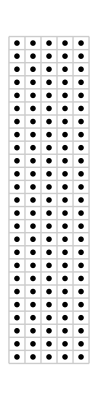

```mathematica
RulePlot[CellularAutomaton[evos[[1, 1]]], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99], 4->RGBColor[0, 0.7000000000000001, 0]}]
```

```mathematica
ArrayPlot[CellularAutomaton[RandomChoice[evos][[1]], RandomInteger[2, 200], 100],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99], 4->RGBColor[0, 0.7000000000000001, 0]}]
```

```mathematica
mr = evos[[1, 1]];
```

```mathematica
mr = {216669022433126270203581211982533285004,4,1};
```

```mathematica
Tuples[{{1}, {2, 3}}]
```

{{1,2},{1,3}}

```mathematica
Most[Select[{{"[◼]", "RuleTuples"}}[5, 1], Length[SequenceCases[#, {0, 0}]]== 1 || # === {0,2, 0}&->"Index"]]
```

```mathematica
Select[{{"[◼]", "RuleTuples"}}[4, 1], Length[SequenceCases[#, {0, 0}]]== 1 &->"Index"]
```

{16,32,48,61,62,63,64}

```mathematica
Most[Select[{{"[◼]", "RuleTuples"}}[4, 1], Count[#, 0]== 2||# === {2, 1, 2} &->"Index"]]
```

{16,26,32,48,52,56,60,61,62}

```mathematica
coms = FromDigits[#, 4]&/@(Tuples[(MapAt[Range[0, 3]&,List/@ IntegerDigits[mr[[1]],4, 4^3] ,List/@Most[Select[{{"[◼]", "RuleTuples"}}[4, 1], Count[#, 0]== 2||# === {2, 1, 2} &->"Index"]]])]);
```

```mathematica
List/@Select[{{"[◼]", "RuleTuples"}}[4, 1], Count[#, 0]==0&->"Index"][[1;;All;;3]]
```

{{1},{5},{9},{17},{21},{25},{33},{37},{41}}

```mathematica
coms = FromDigits[#, 4]&/@(Tuples[(MapAt[Range[0, 3]&,List/@ IntegerDigits[mr[[1]],4, 4^3] ,List/@Select[{{"[◼]", "RuleTuples"}}[4, 1], Count[#, 0]==0&->"Index"][[1;;All;;3]]])]);
```

```mathematica
Length[coms]
```

262144

```mathematica
coms[[1]]
```

216669022274669869617188810868220285964

```mathematica
mr[[1]]
```

216669022433126270203581211982533285004

```mathematica
ArrayPlot[CellularAutomaton[{#, 4, 1}, {{1}, 0}, 110]]&@
```

-Graphics-

```mathematica
out = ParallelMap[
{#, {{"[◼]", "TestLifetime"}}[{#, 4, 1}, 400]}&, coms
];
```

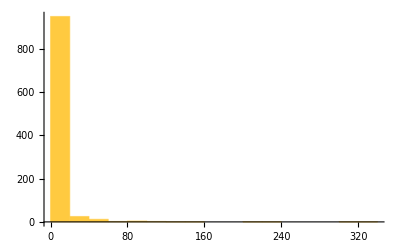

```mathematica
Histogram[out[[All, -1]]/.-Infinity->0]
```

```mathematica
Iconize[out]
```

```mathematica
out = ;
```

```mathematica
ByteCount[out]
```

186824

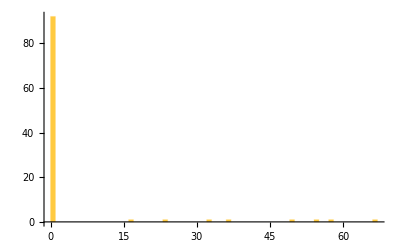

```mathematica
Histogram[RandomSample[out[[All, -1]], 100]/.-Infinity->0, {1}]
```

```mathematica
RandomSample[out[[All, 1]], 3]
```

{302735237105792282122622832578620871820,216665128190753304174270700049584673932,302071921182268898171091543741274838156}

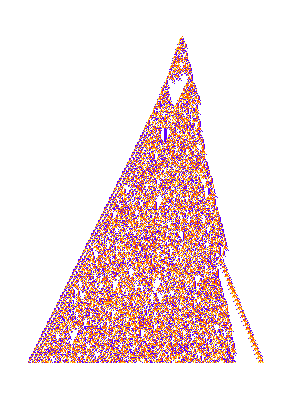
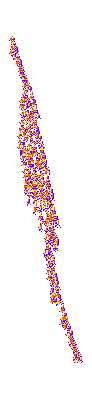
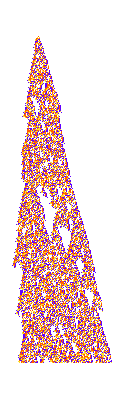
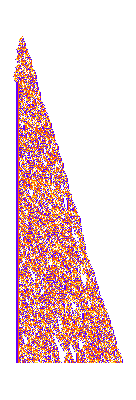
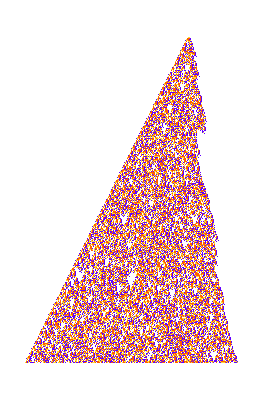
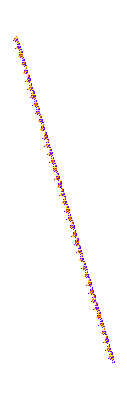
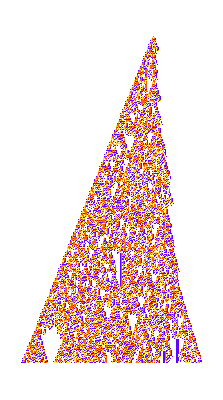
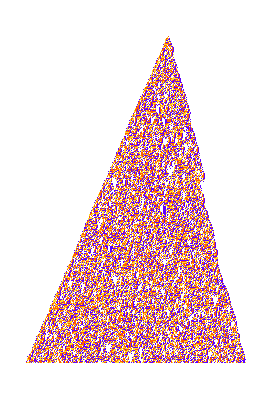

```mathematica
PlotCA[{#, 4, 1}, "Steps"->400]&/@ RandomSample[out[[All, 1]], 8]
```

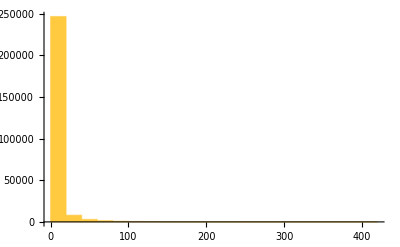

```mathematica
Histogram[out[[All, -1]]/.-Infinity->0]
```

```mathematica
Histogram[out[[All, -1]]/.-Infinity->0]
```

-Graphics-

```mathematica
Length[BinCounts[out[[All, -1]], {10}]]*10
```

400

```mathematica
Count[out[[All, -1]]/.-Infinity->0,x_/;75<x<100]
```

1052

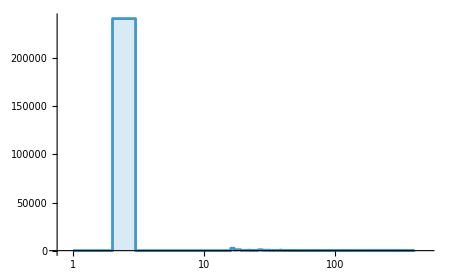

```mathematica
ListStepPlot[BinCounts[out[[All, -1]]/.-Infinity->0, {1}], PlotRange->{{0, 500}, All}, Filling->Bottom, ScalingFunctions->{"Log", Automatic}]
```

```mathematica
Select[out, ]
```

```mathematica
*200
```

37364800

```mathematica
idxs = Select[{{"[◼]", "RuleTuples"}}[4, 1], Count[#, 0]==0&->"Index"][[1;;All;;3]]
```

{1,5,9,17,21,25,33,37,41}

```mathematica
(IntegerDigits[#[[1]], 4, 4^3]&/@getallpointmutations[{out[[1, 1]], 4, 1}])
```

{{1,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{2,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{3,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,0,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,1,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,3,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,1,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,2,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,3,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,0,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,1,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,2,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,1,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,2,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,3,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,1,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,2,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,3,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,1,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,2,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,3,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,1,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,2,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,3,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,1,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,2,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,3,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,0,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,1,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,3,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,0,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,1,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,2,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,0,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,1,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,2,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,0,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,1,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,3,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,0,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,2,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,3,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,1,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,2,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,3,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,0,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,1,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,3,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,1,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,2,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,3,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,0,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,1,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,2,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,0,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,1,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,3,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,1,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,2,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,3,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,1,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,2,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,3,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,0,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,2,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,3,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,0,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,1,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,3,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,0,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,1,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,2,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,1,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,2,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,3,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,0,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,2,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,3,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,0,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,2,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,3,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,0,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,2,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,3,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,1,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,2,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,3,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,0,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,1,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,2,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,0,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,1,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,2,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,1,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,2,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,3,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,1,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,2,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,3,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,0,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,1,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,3,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,0,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,1,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,3,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,0,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,1,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,3,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,1,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,2,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,3,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,1,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,2,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,3,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,0,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,1,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,2,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,0,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,1,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,3,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,1,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,2,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,3,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,0,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,2,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,3,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,0,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,1,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,2,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,0,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,2,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,3,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,1,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,2,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,3,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,0,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,2,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,3,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,0,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,1,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,3,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,0,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,1,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,2,2,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,0,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,1,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,3,2,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,0,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,1,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,3,3,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,0,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,1,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,2,1,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,0,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,2,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,3,0,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,1,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,2,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,3,2,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,0,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,1,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,3,1,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,0,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,2,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,3,0,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,1,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,2,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,3,3,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,0,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,1,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,2,1,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,0,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,2,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,3,1,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,0,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,2,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,3,0,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,1,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,2,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,3,2,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,0,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,1,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,3,0,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,1,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,2,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,3,3,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,0,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,1,0},{0,2,0,3,0,0,0,0,0,2,3,3,2,1,0,2,0,3,2,0,0,1,2,3,0,1,1,1,0,3,3,0,0,2,2,2,0,0,3,2,0,1,3,1,0,1,2,3,2,2,3,1,0,2,1,0,3,1,1,0,2,0,2,0}}

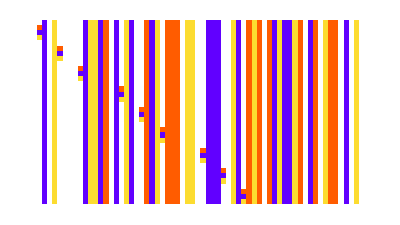

```mathematica
ArrayPlot[(IntegerDigits[#[[1]], 4, 4^3]&/@getallpointmutations[{out[[1, 1]], 4, 1}, idxs])]
```

```mathematica
functional = Select[out, #[[2]]!=-Infinity&];
```

```mathematica
Length[functional]
```

20874

```mathematica
Position[{1, 2, 3}, 1]
```

{{1}}

```mathematica
Lookup[<|a->1|>, b]
```

Missing[KeyAbsent,b]

```mathematica
outa =Association[ParallelMap[#[[1]]->#[[2]]&, out]];
```

```mathematica
functional2 = Select[outa, #!=-Infinity&];
```

```mathematica
funcassoc =
```

```mathematica
Lookup[functional, #]
```

```mathematica
peaks = ParallelSelect[functional, 
With[{ru = #[[1]], life = #[[2]]}, 
AllTrue[
If[MatchQ[#,Missing[__]], True, life>=#]&/@(Lookup[functional2, #]&/@getallpointmutations[{ru, 4, 1}, idxs])]]&->"Index"];
```

$Aborted

```mathematica
With[{ru = #[[1]], life = #[[2]]}, (Lookup[functional2, #[[1]]]&/@getallpointmutations[{ru, 4, 1}, idxs])]&/@ functional[[;;10]]
```

{{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096717958640811825747084],21,Missing[KeyAbsent,46523944769820177975090809608597722252],14,14,14,Missing[KeyAbsent,46523944710399358320847460070733436044],15,Missing[KeyAbsent,46523944710399962783757267385320789132],14,14,14,Missing[KeyAbsent,46523944710399056089410570811949241484],18,Missing[KeyAbsent,46523944710399056089446599608968205452],Missing[KeyAbsent,46523944710399056089392626782183937164],26,Missing[KeyAbsent,46523944710399056089392767519672292492]},{31,40,Missing[KeyAbsent,301735719901102903686923652724754273420],26,26,26,Missing[KeyAbsent,46525242784613689796299829775010419852],Missing[KeyAbsent,46526540858828323503206962399092724876],Missing[KeyAbsent,46527838933042957210114095023175029900],Missing[KeyAbsent,46523944730206096717958781549314102412],38,32,26,26,26,Missing[KeyAbsent,46523944710399358320847600808221791372],Missing[KeyAbsent,46523944710399660552302504465515467916],Missing[KeyAbsent,46523944710399962783757408122809144460],26,26,26,Missing[KeyAbsent,46523944710399056089410711549437596812],Missing[KeyAbsent,46523944710399056089428725947947078796],Missing[KeyAbsent,46523944710399056089446740346456560780],14,Missing[KeyAbsent,46523944710399056089392626782183937164],Missing[KeyAbsent,46523944710399056089392767519672292492]},{26,Missing[KeyAbsent,216665128170868287821097944896577524876],49,16,29,14,Missing[KeyAbsent,46525242784613689796317773804775724172],98,Missing[KeyAbsent,46527838933042957210132039052940334220],Missing[KeyAbsent,46523944730206096717976725579079406732],Missing[KeyAbsent,46523944750013137346542809977465394316],Missing[KeyAbsent,46523944769820177975108894375851381900],35,38,Missing[KeyAbsent,46523944710631169846776649982237004940],40,Missing[KeyAbsent,46523944710399660552320448495280772236],Missing[KeyAbsent,46523944710399962783775352152574448780],52,108,Missing[KeyAbsent,46523944710399056103245699235975582860],Missing[KeyAbsent,46523944710399056089392626782183937164],Missing[KeyAbsent,46523944710399056089428655579202901132],30,Missing[KeyAbsent,46523944710399056089410570811949241484],Missing[KeyAbsent,46523944710399056089410711549437596812],Missing[KeyAbsent,46523944710399056089410781918181774476]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096717994669608844711052],24,Missing[KeyAbsent,46523944769820177975126838405616686220],21,29,Missing[KeyAbsent,46523944710631169846794594012002309260],Missing[KeyAbsent,46523944710399358320883488867752400012],15,Missing[KeyAbsent,46523944710399962783793296182339753100],18,18,18,14,Missing[KeyAbsent,46523944710399056089410570811949241484],Missing[KeyAbsent,46523944710399056089446599608968205452],Missing[KeyAbsent,46523944710399056089428655579202901132],Missing[KeyAbsent,46523944710399056089428725947947078796],Missing[KeyAbsent,46523944710399056089428796316691256460]},{56,Missing[KeyAbsent,216665128170868287821133973693596488844],29,16,Missing[KeyAbsent,47188558708291514025898573507852555404],14,Missing[KeyAbsent,46525242784613689796353802601794688140],Missing[KeyAbsent,46526540858828323503260935225876993164],Missing[KeyAbsent,46527838933042957210168067849959298188],Missing[KeyAbsent,46523944730206096718012754376098370700],338,Missing[KeyAbsent,46523944769820177975144923172870345868],Missing[KeyAbsent,46523944710476427341902006244893578380],Missing[KeyAbsent,46523944710553798594357342512074773644],Missing[KeyAbsent,46523944710631169846812678779255968908],49,Missing[KeyAbsent,46523944710399660552356477292299736204],Missing[KeyAbsent,46523944710399962783811380949593412748],Missing[KeyAbsent,46523944710399056094058355996139771020],Missing[KeyAbsent,46523944710399056098670042014567158924],Missing[KeyAbsent,46523944710399056103281728032994546828],Missing[KeyAbsent,46523944710399056089392626782183937164],51,Missing[KeyAbsent,46523944710399056089428655579202901132],Missing[KeyAbsent,46523944710399056089446599608968205452],Missing[KeyAbsent,46523944710399056089446740346456560780],Missing[KeyAbsent,46523944710399056089446810715200738444]},{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096722570326830253134988],21,Missing[KeyAbsent,46523944769820177979702495627025110156],14,14,14,Missing[KeyAbsent,46523944710399358325459146089160823948],Missing[KeyAbsent,46523944710399660556914049746454500492],Missing[KeyAbsent,46523944710399962788368953403748177036],14,14,14,Missing[KeyAbsent,46523944710399056094022256830376629388],18,Missing[KeyAbsent,46523944710399056094058285627395593356],37,26,Missing[KeyAbsent,46523944710399056094004453538099680396]},{43,Missing[KeyAbsent,216665128170868287825691616516495430796],Missing[KeyAbsent,301735719901102903691535268374437483660],16,Missing[KeyAbsent,47188558708291514030456216330751497356],14,23,Missing[KeyAbsent,46526540858828323507818578048775935116],23,Missing[KeyAbsent,46523944730206096722570397198997312652],28,Missing[KeyAbsent,46523944769820177979702565995769287820],33,59,76,30,30,Missing[KeyAbsent,46523944710399962788369023772492354700],Missing[KeyAbsent,46523944710399056089392626782183937164],Missing[KeyAbsent,46523944710399056098615998819038712972],27,52,Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056094058355996139771020],14,26,Missing[KeyAbsent,46523944710399056094004453538099680396]},{31,40,Missing[KeyAbsent,301735719901102903691535338743181661324],26,26,26,Missing[KeyAbsent,46525242784613689800911515793437807756],Missing[KeyAbsent,46526540858828323507818648417520112780],Missing[KeyAbsent,46527838933042957214725781041602417804],Missing[KeyAbsent,46523944730206096722570467567741490316],38,Missing[KeyAbsent,46523944769820177979702636364513465484],26,26,26,Missing[KeyAbsent,46523944710399358325459286826649179276],Missing[KeyAbsent,46523944710399660556914190483942855820],Missing[KeyAbsent,46523944710399962788369094141236532364],26,26,26,Missing[KeyAbsent,46523944710399056094022397567864984716],Missing[KeyAbsent,46523944710399056094040411966374466700],Missing[KeyAbsent,46523944710399056094058426364883948684],14,37,Missing[KeyAbsent,46523944710399056094004453538099680396]},{58,49,49,16,29,14,Missing[KeyAbsent,46525242784613689800929459823203112076],Missing[KeyAbsent,46526540858828323507836592447285417100],Missing[KeyAbsent,46527838933042957214743725071367722124],Missing[KeyAbsent,46523944730206096722588411597506794636],Missing[KeyAbsent,46523944750013137351154495995892782220],Missing[KeyAbsent,46523944769820177979720580394278769804],Missing[KeyAbsent,46523944710476427346477663466302002316],51,Missing[KeyAbsent,46523944710631169851388336000664392844],43,Missing[KeyAbsent,46523944710399660556932134513708160140],Missing[KeyAbsent,46523944710399962788387038171001836684],51,108,Missing[KeyAbsent,46523944710399056103245699235975582860],37,Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056094058355996139771020],Missing[KeyAbsent,46523944710399056094022256830376629388],Missing[KeyAbsent,46523944710399056094022397567864984716],Missing[KeyAbsent,46523944710399056094022467936609162380]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096722606355627272098956],28,Missing[KeyAbsent,46523944769820177979738524424044074124],34,29,Missing[KeyAbsent,46523944710631169851406280030429697164],Missing[KeyAbsent,46523944710399358325495174886179787916],37,Missing[KeyAbsent,46523944710399962788404982200767141004],18,18,18,14,Missing[KeyAbsent,46523944710399056094022256830376629388],Missing[KeyAbsent,46523944710399056094058285627395593356],Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056094040411966374466700],Missing[KeyAbsent,46523944710399056094040482335118644364]}}

```mathematica
peaks
```

{}

```mathematica
If[MatchQ[#,Missing[__]], True, rulife[[2]]>=#]&/@(Lookup[functional2, #]&/@getallpointmutations[{rulife[[1]], 4, 1}, idxs])
```

True

```mathematica
Missing["KeyAbsent",b]>3
```

Missing[KeyAbsent,b]>3

### Getting peaks

```mathematica
peaks = ParallelSelect[functional[[;;20]],
With[{ru = #[[1]], life = #[[2]]}, 
AllTrue[
(Lookup[functional2, #[[1]]]&/@getallpointmutations[{ru, 4, 1}, idxs]),
MatchQ[#,Missing[__]]|| life>=#&]
]&->"Index"]
```

{}

#### Speeding up algo

```mathematica
With[{ru = #[[1]], life = #[[2]]}, 
AllTrue[
(Lookup[functional2, #[[1]]]&/@getallpointmutations[{ru, 4, 1}, idxs]),
MatchQ[#,Missing[__]]|| life>=#&]
]&/@functional[[;;20]]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
RepeatedTiming[With[{ru = #[[1]], life = #[[2]]}, (Lookup[functional2, #[[1]]]&/@getallpointmutations[{ru, 4, 1}, idxs])]&/@ functional[[;;20]]]
```

{0.00866514,{{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096717958640811825747084],21,Missing[KeyAbsent,46523944769820177975090809608597722252],14,14,14,Missing[KeyAbsent,46523944710399358320847460070733436044],15,Missing[KeyAbsent,46523944710399962783757267385320789132],14,14,14,Missing[KeyAbsent,46523944710399056089410570811949241484],18,Missing[KeyAbsent,46523944710399056089446599608968205452],Missing[KeyAbsent,46523944710399056089392626782183937164],26,Missing[KeyAbsent,46523944710399056089392767519672292492]},{31,40,Missing[KeyAbsent,301735719901102903686923652724754273420],26,26,26,Missing[KeyAbsent,46525242784613689796299829775010419852],Missing[KeyAbsent,46526540858828323503206962399092724876],Missing[KeyAbsent,46527838933042957210114095023175029900],Missing[KeyAbsent,46523944730206096717958781549314102412],38,32,26,26,26,Missing[KeyAbsent,46523944710399358320847600808221791372],Missing[KeyAbsent,46523944710399660552302504465515467916],Missing[KeyAbsent,46523944710399962783757408122809144460],26,26,26,Missing[KeyAbsent,46523944710399056089410711549437596812],Missing[KeyAbsent,46523944710399056089428725947947078796],Missing[KeyAbsent,46523944710399056089446740346456560780],14,Missing[KeyAbsent,46523944710399056089392626782183937164],Missing[KeyAbsent,46523944710399056089392767519672292492]},{26,Missing[KeyAbsent,216665128170868287821097944896577524876],49,16,29,14,Missing[KeyAbsent,46525242784613689796317773804775724172],98,Missing[KeyAbsent,46527838933042957210132039052940334220],Missing[KeyAbsent,46523944730206096717976725579079406732],Missing[KeyAbsent,46523944750013137346542809977465394316],Missing[KeyAbsent,46523944769820177975108894375851381900],35,38,Missing[KeyAbsent,46523944710631169846776649982237004940],40,Missing[KeyAbsent,46523944710399660552320448495280772236],Missing[KeyAbsent,46523944710399962783775352152574448780],52,108,Missing[KeyAbsent,46523944710399056103245699235975582860],Missing[KeyAbsent,46523944710399056089392626782183937164],Missing[KeyAbsent,46523944710399056089428655579202901132],30,Missing[KeyAbsent,46523944710399056089410570811949241484],Missing[KeyAbsent,46523944710399056089410711549437596812],Missing[KeyAbsent,46523944710399056089410781918181774476]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096717994669608844711052],24,Missing[KeyAbsent,46523944769820177975126838405616686220],21,29,Missing[KeyAbsent,46523944710631169846794594012002309260],Missing[KeyAbsent,46523944710399358320883488867752400012],15,Missing[KeyAbsent,46523944710399962783793296182339753100],18,18,18,14,Missing[KeyAbsent,46523944710399056089410570811949241484],Missing[KeyAbsent,46523944710399056089446599608968205452],Missing[KeyAbsent,46523944710399056089428655579202901132],Missing[KeyAbsent,46523944710399056089428725947947078796],Missing[KeyAbsent,46523944710399056089428796316691256460]},{56,Missing[KeyAbsent,216665128170868287821133973693596488844],29,16,Missing[KeyAbsent,47188558708291514025898573507852555404],14,Missing[KeyAbsent,46525242784613689796353802601794688140],Missing[KeyAbsent,46526540858828323503260935225876993164],Missing[KeyAbsent,46527838933042957210168067849959298188],Missing[KeyAbsent,46523944730206096718012754376098370700],338,Missing[KeyAbsent,46523944769820177975144923172870345868],Missing[KeyAbsent,46523944710476427341902006244893578380],Missing[KeyAbsent,46523944710553798594357342512074773644],Missing[KeyAbsent,46523944710631169846812678779255968908],49,Missing[KeyAbsent,46523944710399660552356477292299736204],Missing[KeyAbsent,46523944710399962783811380949593412748],Missing[KeyAbsent,46523944710399056094058355996139771020],Missing[KeyAbsent,46523944710399056098670042014567158924],Missing[KeyAbsent,46523944710399056103281728032994546828],Missing[KeyAbsent,46523944710399056089392626782183937164],51,Missing[KeyAbsent,46523944710399056089428655579202901132],Missing[KeyAbsent,46523944710399056089446599608968205452],Missing[KeyAbsent,46523944710399056089446740346456560780],Missing[KeyAbsent,46523944710399056089446810715200738444]},{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096722570326830253134988],21,Missing[KeyAbsent,46523944769820177979702495627025110156],14,14,14,Missing[KeyAbsent,46523944710399358325459146089160823948],Missing[KeyAbsent,46523944710399660556914049746454500492],Missing[KeyAbsent,46523944710399962788368953403748177036],14,14,14,Missing[KeyAbsent,46523944710399056094022256830376629388],18,Missing[KeyAbsent,46523944710399056094058285627395593356],37,26,Missing[KeyAbsent,46523944710399056094004453538099680396]},{43,Missing[KeyAbsent,216665128170868287825691616516495430796],Missing[KeyAbsent,301735719901102903691535268374437483660],16,Missing[KeyAbsent,47188558708291514030456216330751497356],14,23,Missing[KeyAbsent,46526540858828323507818578048775935116],23,Missing[KeyAbsent,46523944730206096722570397198997312652],28,Missing[KeyAbsent,46523944769820177979702565995769287820],33,59,76,30,30,Missing[KeyAbsent,46523944710399962788369023772492354700],Missing[KeyAbsent,46523944710399056089392626782183937164],Missing[KeyAbsent,46523944710399056098615998819038712972],27,52,Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056094058355996139771020],14,26,Missing[KeyAbsent,46523944710399056094004453538099680396]},{31,40,Missing[KeyAbsent,301735719901102903691535338743181661324],26,26,26,Missing[KeyAbsent,46525242784613689800911515793437807756],Missing[KeyAbsent,46526540858828323507818648417520112780],Missing[KeyAbsent,46527838933042957214725781041602417804],Missing[KeyAbsent,46523944730206096722570467567741490316],38,Missing[KeyAbsent,46523944769820177979702636364513465484],26,26,26,Missing[KeyAbsent,46523944710399358325459286826649179276],Missing[KeyAbsent,46523944710399660556914190483942855820],Missing[KeyAbsent,46523944710399962788369094141236532364],26,26,26,Missing[KeyAbsent,46523944710399056094022397567864984716],Missing[KeyAbsent,46523944710399056094040411966374466700],Missing[KeyAbsent,46523944710399056094058426364883948684],14,37,Missing[KeyAbsent,46523944710399056094004453538099680396]},{58,49,49,16,29,14,Missing[KeyAbsent,46525242784613689800929459823203112076],Missing[KeyAbsent,46526540858828323507836592447285417100],Missing[KeyAbsent,46527838933042957214743725071367722124],Missing[KeyAbsent,46523944730206096722588411597506794636],Missing[KeyAbsent,46523944750013137351154495995892782220],Missing[KeyAbsent,46523944769820177979720580394278769804],Missing[KeyAbsent,46523944710476427346477663466302002316],51,Missing[KeyAbsent,46523944710631169851388336000664392844],43,Missing[KeyAbsent,46523944710399660556932134513708160140],Missing[KeyAbsent,46523944710399962788387038171001836684],51,108,Missing[KeyAbsent,46523944710399056103245699235975582860],37,Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056094058355996139771020],Missing[KeyAbsent,46523944710399056094022256830376629388],Missing[KeyAbsent,46523944710399056094022397567864984716],Missing[KeyAbsent,46523944710399056094022467936609162380]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096722606355627272098956],28,Missing[KeyAbsent,46523944769820177979738524424044074124],34,29,Missing[KeyAbsent,46523944710631169851406280030429697164],Missing[KeyAbsent,46523944710399358325495174886179787916],37,Missing[KeyAbsent,46523944710399962788404982200767141004],18,18,18,14,Missing[KeyAbsent,46523944710399056094022256830376629388],Missing[KeyAbsent,46523944710399056094058285627395593356],Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056094040411966374466700],Missing[KeyAbsent,46523944710399056094040482335118644364]},{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096727182012848680522892],21,Missing[KeyAbsent,46523944769820177984314181645452498060],14,14,14,Missing[KeyAbsent,46523944710399358330070832107588211852],17,Missing[KeyAbsent,46523944710399962792980639422175564940],14,14,14,Missing[KeyAbsent,46523944710399056098633942848804017292],18,Missing[KeyAbsent,46523944710399056098669971645822981260],Missing[KeyAbsent,46523944710399056098615998819038712972],26,Missing[KeyAbsent,46523944710399056098616139556527068300]},{31,40,Missing[KeyAbsent,301735719901102903696147024761609049228],26,26,26,Missing[KeyAbsent,46525242784613689805523201811865195660],Missing[KeyAbsent,46526540858828323512430334435947500684],Missing[KeyAbsent,46527838933042957219337467060029805708],Missing[KeyAbsent,46523944730206096727182153586168878220],38,Missing[KeyAbsent,46523944769820177984314322382940853388],26,26,26,Missing[KeyAbsent,46523944710399358330070972845076567180],Missing[KeyAbsent,46523944710399660561525876502370243724],Missing[KeyAbsent,46523944710399962792980780159663920268],26,26,26,Missing[KeyAbsent,46523944710399056098634083586292372620],Missing[KeyAbsent,46523944710399056098652097984801854604],45,14,Missing[KeyAbsent,46523944710399056098615998819038712972],Missing[KeyAbsent,46523944710399056098616139556527068300]},{Missing[KeyAbsent,131594536440633671964477665075490247820],Missing[KeyAbsent,216665128170868287830321316933432300684],188,16,29,14,Missing[KeyAbsent,46525242784613689805541145841630499980],Missing[KeyAbsent,46526540858828323512448278465712805004],Missing[KeyAbsent,46527838933042957219355411089795110028],Missing[KeyAbsent,46523944730206096727200097615934182540],Missing[KeyAbsent,46523944750013137355766182014320170124],Missing[KeyAbsent,46523944769820177984332266412706157708],Missing[KeyAbsent,46523944710476427351089349484729390220],Missing[KeyAbsent,46523944710553798603544685751910585484],Missing[KeyAbsent,46523944710631169856000022019091780748],28,32,Missing[KeyAbsent,46523944710399962792998724189429224588],51,52,Missing[KeyAbsent,46523944710399056103245699235975582860],Missing[KeyAbsent,46523944710399056098615998819038712972],Missing[KeyAbsent,46523944710399056098652027616057676940],Missing[KeyAbsent,46523944710399056098670042014567158924],Missing[KeyAbsent,46523944710399056098633942848804017292],Missing[KeyAbsent,46523944710399056098634083586292372620],Missing[KeyAbsent,46523944710399056098634153955036550284]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096727218041645699486860],117,Missing[KeyAbsent,46523944769820177984350210442471462028],Missing[KeyAbsent,46523944710476427351107293514494694540],29,Missing[KeyAbsent,46523944710631169856017966048857085068],Missing[KeyAbsent,46523944710399358330106860904607175820],17,Missing[KeyAbsent,46523944710399962793016668219194528908],18,18,18,14,Missing[KeyAbsent,46523944710399056098633942848804017292],Missing[KeyAbsent,46523944710399056098669971645822981260],Missing[KeyAbsent,46523944710399056098652027616057676940],Missing[KeyAbsent,46523944710399056098652097984801854604],Missing[KeyAbsent,46523944710399056098652168353546032268]},{47,54,45,Missing[KeyAbsent,46856251709345285066896064148381422732],Missing[KeyAbsent,47188558708291514035122015913451508876],36,Missing[KeyAbsent,46525242784613689805577245007393641612],Missing[KeyAbsent,46526540858828323512484377631475946636],Missing[KeyAbsent,46527838933042957219391510255558251660],Missing[KeyAbsent,46523944730206096727236196781697324172],Missing[KeyAbsent,46523944750013137355802281180083311756],Missing[KeyAbsent,46523944769820177984368365578469299340],Missing[KeyAbsent,46523944710476427351125448650492531852],Missing[KeyAbsent,46523944710553798603580784917673727116],Missing[KeyAbsent,46523944710631169856036121184854922380],Missing[KeyAbsent,46523944710399358330125016040605013132],Missing[KeyAbsent,46523944710399660561579919697898689676],Missing[KeyAbsent,46523944710399962793034823355192366220],Missing[KeyAbsent,46523944710399056089446740346456560780],Missing[KeyAbsent,46523944710399056094058426364883948684],Missing[KeyAbsent,46523944710399056103281798401738724492],26,Missing[KeyAbsent,46523944710399056098634083586292372620],Missing[KeyAbsent,46523944710399056098652097984801854604],Missing[KeyAbsent,46523944710399056098669971645822981260],Missing[KeyAbsent,46523944710399056098670042014567158924],Missing[KeyAbsent,46523944710399056098670182752055514252]},{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096731793698867107910796],21,Missing[KeyAbsent,46523944769820177988925867663879885964],14,14,14,Missing[KeyAbsent,46523944710399358334682518126015599756],26,Missing[KeyAbsent,46523944710399962797592325440602952844],14,14,14,Missing[KeyAbsent,46523944710399056103245628867231405196],18,Missing[KeyAbsent,46523944710399056103281657664250369164],27,26,Missing[KeyAbsent,46523944710399056103227825574954456204]},{Missing[KeyAbsent,131594536440633671969071336695408153740],50,Missing[KeyAbsent,301735719901102903700758640411292259468],16,49,14,24,69,Missing[KeyAbsent,46527838933042957223949082709713015948],Missing[KeyAbsent,46523944730206096731793769235852088460],28,Missing[KeyAbsent,46523944769820177988925938032624063628],27,27,27,23,26,26,Missing[KeyAbsent,46523944710399056089392626782183937164],37,Missing[KeyAbsent,46523944710399056098615998819038712972],Missing[KeyAbsent,46523944710399056103245699235975582860],34,Missing[KeyAbsent,46523944710399056103281728032994546828],14,26,Missing[KeyAbsent,46523944710399056103227825574954456204]},{31,40,Missing[KeyAbsent,301735719901102903700758710780036437132],26,26,26,Missing[KeyAbsent,46525242784613689810134887830292583564],30,Missing[KeyAbsent,46527838933042957223949153078457193612],Missing[KeyAbsent,46523944730206096731793839604596266124],38,24,26,26,26,Missing[KeyAbsent,46523944710399358334682658863503955084],Missing[KeyAbsent,46523944710399660566137562520797631628],48,26,26,26,Missing[KeyAbsent,46523944710399056103245769604719760524],Missing[KeyAbsent,46523944710399056103263784003229242508],Missing[KeyAbsent,46523944710399056103281798401738724492],14,27,Missing[KeyAbsent,46523944710399056103227825574954456204]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096731829727664126874764],Missing[KeyAbsent,46523944750013137360395812062512862348],89,Missing[KeyAbsent,46523944710476427355718979532922082444],29,Missing[KeyAbsent,46523944710631169860629652067284472972],Missing[KeyAbsent,46523944710399358334718546923034563724],Missing[KeyAbsent,46523944710399660566173450580328240268],Missing[KeyAbsent,46523944710399962797628354237621916812],18,18,18,14,Missing[KeyAbsent,46523944710399056103245628867231405196],Missing[KeyAbsent,46523944710399056103281657664250369164],34,Missing[KeyAbsent,46523944710399056103263784003229242508],Missing[KeyAbsent,46523944710399056103263854371973420172]},{28,36,69,16,Missing[KeyAbsent,47188558708291514039715617164625237132],14,Missing[KeyAbsent,46525242784613689810170846258567369868],24,34,Missing[KeyAbsent,46523944730206096731829798032871052428],165,Missing[KeyAbsent,46523944769820177988961966829643027596],26,40,Missing[KeyAbsent,46523944710631169860629722436028650636],26,24,26,Missing[KeyAbsent,46523944710399056089428655579202901132],Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056098652027616057676940],27,Missing[KeyAbsent,46523944710399056103245699235975582860],Missing[KeyAbsent,46523944710399056103281728032994546828],18,Missing[KeyAbsent,46523944710399056103263784003229242508],Missing[KeyAbsent,46523944710399056103263854371973420172]}}}

```mathematica
RepeatedTiming[getallpointmutations[{#[[1]], 4, 1}, idxs]&/@ functional[[;;1000]]]
```

```mathematica
RepeatedTiming[getallpointmutations[{#[[1]], 4, 1}, idxs]&/@ functional[[;;20]]]
```

```mathematica
RepeatedTiming[Map[Lookup[functional2, #[[1]]]&,[[2]], {2}]]
```

{0.000586112,{{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096717958640811825747084],21,Missing[KeyAbsent,46523944769820177975090809608597722252],14,14,14,Missing[KeyAbsent,46523944710399358320847460070733436044],15,Missing[KeyAbsent,46523944710399962783757267385320789132],14,14,14,Missing[KeyAbsent,46523944710399056089410570811949241484],18,Missing[KeyAbsent,46523944710399056089446599608968205452],Missing[KeyAbsent,46523944710399056089392626782183937164],26,Missing[KeyAbsent,46523944710399056089392767519672292492]},{31,40,Missing[KeyAbsent,301735719901102903686923652724754273420],26,26,26,Missing[KeyAbsent,46525242784613689796299829775010419852],Missing[KeyAbsent,46526540858828323503206962399092724876],Missing[KeyAbsent,46527838933042957210114095023175029900],Missing[KeyAbsent,46523944730206096717958781549314102412],38,32,26,26,26,Missing[KeyAbsent,46523944710399358320847600808221791372],Missing[KeyAbsent,46523944710399660552302504465515467916],Missing[KeyAbsent,46523944710399962783757408122809144460],26,26,26,Missing[KeyAbsent,46523944710399056089410711549437596812],Missing[KeyAbsent,46523944710399056089428725947947078796],Missing[KeyAbsent,46523944710399056089446740346456560780],14,Missing[KeyAbsent,46523944710399056089392626782183937164],Missing[KeyAbsent,46523944710399056089392767519672292492]},{26,Missing[KeyAbsent,216665128170868287821097944896577524876],49,16,29,14,Missing[KeyAbsent,46525242784613689796317773804775724172],98,Missing[KeyAbsent,46527838933042957210132039052940334220],Missing[KeyAbsent,46523944730206096717976725579079406732],Missing[KeyAbsent,46523944750013137346542809977465394316],Missing[KeyAbsent,46523944769820177975108894375851381900],35,38,Missing[KeyAbsent,46523944710631169846776649982237004940],40,Missing[KeyAbsent,46523944710399660552320448495280772236],Missing[KeyAbsent,46523944710399962783775352152574448780],52,108,Missing[KeyAbsent,46523944710399056103245699235975582860],Missing[KeyAbsent,46523944710399056089392626782183937164],Missing[KeyAbsent,46523944710399056089428655579202901132],30,Missing[KeyAbsent,46523944710399056089410570811949241484],Missing[KeyAbsent,46523944710399056089410711549437596812],Missing[KeyAbsent,46523944710399056089410781918181774476]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096717994669608844711052],24,Missing[KeyAbsent,46523944769820177975126838405616686220],21,29,Missing[KeyAbsent,46523944710631169846794594012002309260],Missing[KeyAbsent,46523944710399358320883488867752400012],15,Missing[KeyAbsent,46523944710399962783793296182339753100],18,18,18,14,Missing[KeyAbsent,46523944710399056089410570811949241484],Missing[KeyAbsent,46523944710399056089446599608968205452],Missing[KeyAbsent,46523944710399056089428655579202901132],Missing[KeyAbsent,46523944710399056089428725947947078796],Missing[KeyAbsent,46523944710399056089428796316691256460]},{56,Missing[KeyAbsent,216665128170868287821133973693596488844],29,16,Missing[KeyAbsent,47188558708291514025898573507852555404],14,Missing[KeyAbsent,46525242784613689796353802601794688140],Missing[KeyAbsent,46526540858828323503260935225876993164],Missing[KeyAbsent,46527838933042957210168067849959298188],Missing[KeyAbsent,46523944730206096718012754376098370700],338,Missing[KeyAbsent,46523944769820177975144923172870345868],Missing[KeyAbsent,46523944710476427341902006244893578380],Missing[KeyAbsent,46523944710553798594357342512074773644],Missing[KeyAbsent,46523944710631169846812678779255968908],49,Missing[KeyAbsent,46523944710399660552356477292299736204],Missing[KeyAbsent,46523944710399962783811380949593412748],Missing[KeyAbsent,46523944710399056094058355996139771020],Missing[KeyAbsent,46523944710399056098670042014567158924],Missing[KeyAbsent,46523944710399056103281728032994546828],Missing[KeyAbsent,46523944710399056089392626782183937164],51,Missing[KeyAbsent,46523944710399056089428655579202901132],Missing[KeyAbsent,46523944710399056089446599608968205452],Missing[KeyAbsent,46523944710399056089446740346456560780],Missing[KeyAbsent,46523944710399056089446810715200738444]},{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096722570326830253134988],21,Missing[KeyAbsent,46523944769820177979702495627025110156],14,14,14,Missing[KeyAbsent,46523944710399358325459146089160823948],Missing[KeyAbsent,46523944710399660556914049746454500492],Missing[KeyAbsent,46523944710399962788368953403748177036],14,14,14,Missing[KeyAbsent,46523944710399056094022256830376629388],18,Missing[KeyAbsent,46523944710399056094058285627395593356],37,26,Missing[KeyAbsent,46523944710399056094004453538099680396]},{43,Missing[KeyAbsent,216665128170868287825691616516495430796],Missing[KeyAbsent,301735719901102903691535268374437483660],16,Missing[KeyAbsent,47188558708291514030456216330751497356],14,23,Missing[KeyAbsent,46526540858828323507818578048775935116],23,Missing[KeyAbsent,46523944730206096722570397198997312652],28,Missing[KeyAbsent,46523944769820177979702565995769287820],33,59,76,30,30,Missing[KeyAbsent,46523944710399962788369023772492354700],Missing[KeyAbsent,46523944710399056089392626782183937164],Missing[KeyAbsent,46523944710399056098615998819038712972],27,52,Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056094058355996139771020],14,26,Missing[KeyAbsent,46523944710399056094004453538099680396]},{31,40,Missing[KeyAbsent,301735719901102903691535338743181661324],26,26,26,Missing[KeyAbsent,46525242784613689800911515793437807756],Missing[KeyAbsent,46526540858828323507818648417520112780],Missing[KeyAbsent,46527838933042957214725781041602417804],Missing[KeyAbsent,46523944730206096722570467567741490316],38,Missing[KeyAbsent,46523944769820177979702636364513465484],26,26,26,Missing[KeyAbsent,46523944710399358325459286826649179276],Missing[KeyAbsent,46523944710399660556914190483942855820],Missing[KeyAbsent,46523944710399962788369094141236532364],26,26,26,Missing[KeyAbsent,46523944710399056094022397567864984716],Missing[KeyAbsent,46523944710399056094040411966374466700],Missing[KeyAbsent,46523944710399056094058426364883948684],14,37,Missing[KeyAbsent,46523944710399056094004453538099680396]},{58,49,49,16,29,14,Missing[KeyAbsent,46525242784613689800929459823203112076],Missing[KeyAbsent,46526540858828323507836592447285417100],Missing[KeyAbsent,46527838933042957214743725071367722124],Missing[KeyAbsent,46523944730206096722588411597506794636],Missing[KeyAbsent,46523944750013137351154495995892782220],Missing[KeyAbsent,46523944769820177979720580394278769804],Missing[KeyAbsent,46523944710476427346477663466302002316],51,Missing[KeyAbsent,46523944710631169851388336000664392844],43,Missing[KeyAbsent,46523944710399660556932134513708160140],Missing[KeyAbsent,46523944710399962788387038171001836684],51,108,Missing[KeyAbsent,46523944710399056103245699235975582860],37,Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056094058355996139771020],Missing[KeyAbsent,46523944710399056094022256830376629388],Missing[KeyAbsent,46523944710399056094022397567864984716],Missing[KeyAbsent,46523944710399056094022467936609162380]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096722606355627272098956],28,Missing[KeyAbsent,46523944769820177979738524424044074124],34,29,Missing[KeyAbsent,46523944710631169851406280030429697164],Missing[KeyAbsent,46523944710399358325495174886179787916],37,Missing[KeyAbsent,46523944710399962788404982200767141004],18,18,18,14,Missing[KeyAbsent,46523944710399056094022256830376629388],Missing[KeyAbsent,46523944710399056094058285627395593356],Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056094040411966374466700],Missing[KeyAbsent,46523944710399056094040482335118644364]},{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096727182012848680522892],21,Missing[KeyAbsent,46523944769820177984314181645452498060],14,14,14,Missing[KeyAbsent,46523944710399358330070832107588211852],17,Missing[KeyAbsent,46523944710399962792980639422175564940],14,14,14,Missing[KeyAbsent,46523944710399056098633942848804017292],18,Missing[KeyAbsent,46523944710399056098669971645822981260],Missing[KeyAbsent,46523944710399056098615998819038712972],26,Missing[KeyAbsent,46523944710399056098616139556527068300]},{31,40,Missing[KeyAbsent,301735719901102903696147024761609049228],26,26,26,Missing[KeyAbsent,46525242784613689805523201811865195660],Missing[KeyAbsent,46526540858828323512430334435947500684],Missing[KeyAbsent,46527838933042957219337467060029805708],Missing[KeyAbsent,46523944730206096727182153586168878220],38,Missing[KeyAbsent,46523944769820177984314322382940853388],26,26,26,Missing[KeyAbsent,46523944710399358330070972845076567180],Missing[KeyAbsent,46523944710399660561525876502370243724],Missing[KeyAbsent,46523944710399962792980780159663920268],26,26,26,Missing[KeyAbsent,46523944710399056098634083586292372620],Missing[KeyAbsent,46523944710399056098652097984801854604],45,14,Missing[KeyAbsent,46523944710399056098615998819038712972],Missing[KeyAbsent,46523944710399056098616139556527068300]},{Missing[KeyAbsent,131594536440633671964477665075490247820],Missing[KeyAbsent,216665128170868287830321316933432300684],188,16,29,14,Missing[KeyAbsent,46525242784613689805541145841630499980],Missing[KeyAbsent,46526540858828323512448278465712805004],Missing[KeyAbsent,46527838933042957219355411089795110028],Missing[KeyAbsent,46523944730206096727200097615934182540],Missing[KeyAbsent,46523944750013137355766182014320170124],Missing[KeyAbsent,46523944769820177984332266412706157708],Missing[KeyAbsent,46523944710476427351089349484729390220],Missing[KeyAbsent,46523944710553798603544685751910585484],Missing[KeyAbsent,46523944710631169856000022019091780748],28,32,Missing[KeyAbsent,46523944710399962792998724189429224588],51,52,Missing[KeyAbsent,46523944710399056103245699235975582860],Missing[KeyAbsent,46523944710399056098615998819038712972],Missing[KeyAbsent,46523944710399056098652027616057676940],Missing[KeyAbsent,46523944710399056098670042014567158924],Missing[KeyAbsent,46523944710399056098633942848804017292],Missing[KeyAbsent,46523944710399056098634083586292372620],Missing[KeyAbsent,46523944710399056098634153955036550284]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096727218041645699486860],117,Missing[KeyAbsent,46523944769820177984350210442471462028],Missing[KeyAbsent,46523944710476427351107293514494694540],29,Missing[KeyAbsent,46523944710631169856017966048857085068],Missing[KeyAbsent,46523944710399358330106860904607175820],17,Missing[KeyAbsent,46523944710399962793016668219194528908],18,18,18,14,Missing[KeyAbsent,46523944710399056098633942848804017292],Missing[KeyAbsent,46523944710399056098669971645822981260],Missing[KeyAbsent,46523944710399056098652027616057676940],Missing[KeyAbsent,46523944710399056098652097984801854604],Missing[KeyAbsent,46523944710399056098652168353546032268]},{47,54,45,Missing[KeyAbsent,46856251709345285066896064148381422732],Missing[KeyAbsent,47188558708291514035122015913451508876],36,Missing[KeyAbsent,46525242784613689805577245007393641612],Missing[KeyAbsent,46526540858828323512484377631475946636],Missing[KeyAbsent,46527838933042957219391510255558251660],Missing[KeyAbsent,46523944730206096727236196781697324172],Missing[KeyAbsent,46523944750013137355802281180083311756],Missing[KeyAbsent,46523944769820177984368365578469299340],Missing[KeyAbsent,46523944710476427351125448650492531852],Missing[KeyAbsent,46523944710553798603580784917673727116],Missing[KeyAbsent,46523944710631169856036121184854922380],Missing[KeyAbsent,46523944710399358330125016040605013132],Missing[KeyAbsent,46523944710399660561579919697898689676],Missing[KeyAbsent,46523944710399962793034823355192366220],Missing[KeyAbsent,46523944710399056089446740346456560780],Missing[KeyAbsent,46523944710399056094058426364883948684],Missing[KeyAbsent,46523944710399056103281798401738724492],26,Missing[KeyAbsent,46523944710399056098634083586292372620],Missing[KeyAbsent,46523944710399056098652097984801854604],Missing[KeyAbsent,46523944710399056098669971645822981260],Missing[KeyAbsent,46523944710399056098670042014567158924],Missing[KeyAbsent,46523944710399056098670182752055514252]},{25,19,24,14,14,14,14,14,14,Missing[KeyAbsent,46523944730206096731793698867107910796],21,Missing[KeyAbsent,46523944769820177988925867663879885964],14,14,14,Missing[KeyAbsent,46523944710399358334682518126015599756],26,Missing[KeyAbsent,46523944710399962797592325440602952844],14,14,14,Missing[KeyAbsent,46523944710399056103245628867231405196],18,Missing[KeyAbsent,46523944710399056103281657664250369164],27,26,Missing[KeyAbsent,46523944710399056103227825574954456204]},{Missing[KeyAbsent,131594536440633671969071336695408153740],50,Missing[KeyAbsent,301735719901102903700758640411292259468],16,49,14,24,69,Missing[KeyAbsent,46527838933042957223949082709713015948],Missing[KeyAbsent,46523944730206096731793769235852088460],28,Missing[KeyAbsent,46523944769820177988925938032624063628],27,27,27,23,26,26,Missing[KeyAbsent,46523944710399056089392626782183937164],37,Missing[KeyAbsent,46523944710399056098615998819038712972],Missing[KeyAbsent,46523944710399056103245699235975582860],34,Missing[KeyAbsent,46523944710399056103281728032994546828],14,26,Missing[KeyAbsent,46523944710399056103227825574954456204]},{31,40,Missing[KeyAbsent,301735719901102903700758710780036437132],26,26,26,Missing[KeyAbsent,46525242784613689810134887830292583564],30,Missing[KeyAbsent,46527838933042957223949153078457193612],Missing[KeyAbsent,46523944730206096731793839604596266124],38,24,26,26,26,Missing[KeyAbsent,46523944710399358334682658863503955084],Missing[KeyAbsent,46523944710399660566137562520797631628],48,26,26,26,Missing[KeyAbsent,46523944710399056103245769604719760524],Missing[KeyAbsent,46523944710399056103263784003229242508],Missing[KeyAbsent,46523944710399056103281798401738724492],14,27,Missing[KeyAbsent,46523944710399056103227825574954456204]},{18,18,18,18,18,18,18,18,18,Missing[KeyAbsent,46523944730206096731829727664126874764],Missing[KeyAbsent,46523944750013137360395812062512862348],89,Missing[KeyAbsent,46523944710476427355718979532922082444],29,Missing[KeyAbsent,46523944710631169860629652067284472972],Missing[KeyAbsent,46523944710399358334718546923034563724],Missing[KeyAbsent,46523944710399660566173450580328240268],Missing[KeyAbsent,46523944710399962797628354237621916812],18,18,18,14,Missing[KeyAbsent,46523944710399056103245628867231405196],Missing[KeyAbsent,46523944710399056103281657664250369164],34,Missing[KeyAbsent,46523944710399056103263784003229242508],Missing[KeyAbsent,46523944710399056103263854371973420172]},{28,36,69,16,Missing[KeyAbsent,47188558708291514039715617164625237132],14,Missing[KeyAbsent,46525242784613689810170846258567369868],24,34,Missing[KeyAbsent,46523944730206096731829798032871052428],165,Missing[KeyAbsent,46523944769820177988961966829643027596],26,40,Missing[KeyAbsent,46523944710631169860629722436028650636],26,24,26,Missing[KeyAbsent,46523944710399056089428655579202901132],Missing[KeyAbsent,46523944710399056094040341597630289036],Missing[KeyAbsent,46523944710399056098652027616057676940],27,Missing[KeyAbsent,46523944710399056103245699235975582860],Missing[KeyAbsent,46523944710399056103281728032994546828],18,Missing[KeyAbsent,46523944710399056103263784003229242508],Missing[KeyAbsent,46523944710399056103263854371973420172]}}}

```mathematica
Module[{n = functional[[1, 1, 1]], k =  4, r = 1,digits, mudigs},
digits =  List/@IntegerDigits[n, k, k^(2r+1)];
mudigs =(Tuples[ReplacePart[digits, #->{Delete[Range[0, k - 1], digits[[#]]]}]]&/@ Range[Length[digits]-1][[idxs]] )// Flatten[#, 1]&;
{#, k, r}&/@ (FromDigits[#, k]&/@ mudigs)
  ]
```

```mathematica
k = 4; r = 1;
```

```mathematica
RepeatedTiming[alldigits = Function[n, List/@IntegerDigits[n, k, k^(2r+1)]]/@ functional[[;;1000, 1]]]
```

```mathematica
RepeatedTiming[Function[digs, (Tuples[ReplacePart[digs, #->{Delete[Range[0, k - 1], digs[[#]]]}]]&/@ Range[Length[digs]-1][[idxs]] )// Flatten[#, 1]&]/@ alldigits]
```

```mathematica
RepeatedTiming[Function[digs, 
ReplacePart[digs, #->{Delete[Range[0, k - 1], digs[[#]]]}]&/@Range[Length[digs]-1][[idxs]] ]/@alldigits]
```

```mathematica
Function[digs, 
ReplacePart[digs, #->{Delete[Range[0, k - 1], digs[[#]]]}]&/@Range[Length[digs]-1][[idxs]] ]/@alldigits
```

```mathematica
RepeatedTiming[Map[Tuples, , {2}]]
```

```mathematica
Length[Flatten[[[2]]]]
```

1474840

```mathematica
Length[idxs]
```

9

```mathematica
RepeatedTiming[a = Table[Tuples[Range[0, 3], 9], 10];]
```

{0.0500708,Null}

#### LLM Garbage

```mathematica
getAllPointMutations[{n_,k_,r_},idxs_:All]:=Module[{digits,len,weights,positions},(*1) get fixed‑length digit list*)digits=IntegerDigits[n,k,2*r+1];
len=Length[digits];
(*2) precompute the positional weights for each digit slot*)weights=k^Range[len-1,0,-1];
(*3) decide which positions to mutate*)positions=If[idxs===All,Range[len],idxs];
(*4) for each position i,for each alternative digit d,compute n+(d-digits[[i]])*weights[[i]] directly*)Flatten[Table[n+(d-digits[[i]]) weights[[i]],{i,positions},{d,DeleteCases[Range[0,k-1],digits[[i]]]}],1]]
```

```mathematica
getAllPointMutations[{#[[1]], 4, 1}, idxs]&/@ functional[[{1}]]
```

Part::partw: Part 5 of {0,3,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{46523944710399056089392556413439759516,46523944710399056089392556413439759532,46523944710399056089392556413439759548,46523944710399056089392556413439759500-{0,3,0}⟦5⟧ {16,4,1}⟦5⟧,46523944710399056089392556413439759500+(1-{0,3,0}⟦5⟧) {16,4,1}⟦5⟧,46523944710399056089392556413439759500+(2-{0,3,0}⟦5⟧) {16,4,1}⟦5⟧,46523944710399056089392556413439759500+(3-{0,3,0}⟦5⟧) {16,4,1}⟦5⟧,46523944710399056089392556413439759500-{0,3,0}⟦9⟧ {16,4,1}⟦9⟧,46523944710399056089392556413439759500+(1-{0,3,0}⟦9⟧) {16,4,1}⟦9⟧,46523944710399056089392556413439759500+(2-{0,3,0}⟦9⟧) {16,4,1}⟦9⟧,46523944710399056089392556413439759500+(3-{0,3,0}⟦9⟧) {16,4,1}⟦9⟧,46523944710399056089392556413439759500-{0,3,0}⟦17⟧ {16,4,1}⟦17⟧,46523944710399056089392556413439759500+(1-{0,3,0}⟦17⟧) {16,4,1}⟦17⟧,46523944710399056089392556413439759500+(2-{0,3,0}⟦17⟧) {16,4,1}⟦17⟧,46523944710399056089392556413439759500+(3-{0,3,0}⟦17⟧) {16,4,1}⟦17⟧,46523944710399056089392556413439759500-{0,3,0}⟦21⟧ {16,4,1}⟦21⟧,46523944710399056089392556413439759500+(1-{0,3,0}⟦21⟧) {16,4,1}⟦21⟧,46523944710399056089392556413439759500+(2-{0,3,0}⟦21⟧) {16,4,1}⟦21⟧,46523944710399056089392556413439759500+(3-{0,3,0}⟦21⟧) {16,4,1}⟦21⟧,46523944710399056089392556413439759500-{0,3,0}⟦25⟧ {16,4,1}⟦25⟧,46523944710399056089392556413439759500+(1-{0,3,0}⟦25⟧) {16,4,1}⟦25⟧,46523944710399056089392556413439759500+(2-{0,3,0}⟦25⟧) {16,4,1}⟦25⟧,46523944710399056089392556413439759500+(3-{0,3,0}⟦25⟧) {16,4,1}⟦25⟧,46523944710399056089392556413439759500-{0,3,0}⟦33⟧ {16,4,1}⟦33⟧,46523944710399056089392556413439759500+(1-{0,3,0}⟦33⟧) {16,4,1}⟦33⟧,46523944710399056089392556413439759500+(2-{0,3,0}⟦33⟧) {16,4,1}⟦33⟧,46523944710399056089392556413439759500+(3-{0,3,0}⟦33⟧) {16,4,1}⟦33⟧,46523944710399056089392556413439759500-{0,3,0}⟦37⟧ {16,4,1}⟦37⟧,46523944710399056089392556413439759500+(1-{0,3,0}⟦37⟧) {16,4,1}⟦37⟧,46523944710399056089392556413439759500+(2-{0,3,0}⟦37⟧) {16,4,1}⟦37⟧,46523944710399056089392556413439759500+(3-{0,3,0}⟦37⟧) {16,4,1}⟦37⟧,46523944710399056089392556413439759500-{0,3,0}⟦41⟧ {16,4,1}⟦41⟧,46523944710399056089392556413439759500+(1-{0,3,0}⟦41⟧) {16,4,1}⟦41⟧,46523944710399056089392556413439759500+(2-{0,3,0}⟦41⟧) {16,4,1}⟦41⟧,46523944710399056089392556413439759500+(3-{0,3,0}⟦41⟧) {16,4,1}⟦41⟧}}

```mathematica
RepeatedTiming[getAllPointMutations[{#[[1]], 4, 1}, idxs]&/@ functional[[;;100]]]
```

Part::partw: Part 5 of {0,3,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
RepeatedTiming[getallpointmutations[{#[[1]], 4, 1}, idxs]&/@ functional[[;;100]]]
```

```mathematica
getAllPointMutations[{n_,k_,r_},idxs_ : All]:=
  Module[{digits,len,weights,positions,altDigits},
    (* Get fixed-length digit list *)
    digits=IntegerDigits[n,k,2*r+1];
    len=Length[digits];
    (* Precompute positional weights *)
    weights=k^Range[len-1,0,-1];
    (* Decide which positions to mutate *)
    positions=If[idxs===All,Range[len],idxs];
    (* Generate alternative digits for each position *)
    altDigits=Table[
      DeleteCases[Range[0,k-1],digits[[i]]],
      {i,positions}
    ];
    (* Create tuples in parallel *)
    ParallelTable[
      Flatten[
        Table[
          digits[[i]]=d; 
          FromDigits[digits,k],
          {d,altDigits[[i]]}
        ],
        1
      ],
      {i,Length[positions]}
    ]
  ]
```

#### Speeding up algo 2

Just get matrix of interactions

```mathematica
mutemat = SparseArray[Outer[Boole[Count[Unitize[Subtract@@(IntegerDigits[#, 4, 4^3]&/@{#1, #2})], 1] == 1]&, functional[[All, 1]], functional[[All, 1]]]];
```

```mathematica
mutemat = SparseArray[ParallelTable[Boole[Count[Unitize[Subtract@@(IntegerDigits[#, 4, 4^3]&/@{#1, #2})], 1] == 1]&, {i, 1, Length[functional] - 1}, {j, i + 1, Length[functional]}]];
```

```mathematica
Module[{digs},
SparseArray[ParallelTable[
digs = IntegerDigits[functional[[i, 1]],  4, 4^3];
Boole[Count[Unitize[digs - IntegerDigits[functional[[j, 1]],  4, 4^3]]]==1],
{i, 1, Length[functional[[;;3]]] - 1}, {j, i + 1, Length[functional[[;;3]]]}]]]
```

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in SparseArray[{{Boole[Count[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,«14»}]==1],Boole[Count[{0,0,0,0,0,0,0,0,«35»,0,0,0,0,0,0,0,«14»}]==1]},{«1»}}].

```mathematica
mutemat = Module[{digs},
ParallelTable[
digs = IntegerDigits[functional[[i, 1]],  4, 4^3];
Boole[Count[Unitize[digs - IntegerDigits[functional[[j, 1]],  4, 4^3]], 1]==1],
{i, 1, Length[functional[[;;100]]] - 1}, {j, i + 1, Length[functional[[;;100]]]}]];
```

```mathematica
maxLen=Max[Length/@mutemat];
rectangularMat=PadRight[#,maxLen]&/@mutemat;
```

```mathematica
ByteCount[rectangularMat]
```

240016

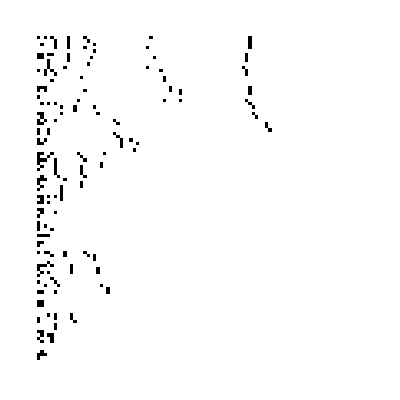

```mathematica
ArrayPlot[mutemat]
```

```mathematica
ArrayPlot[SparseArray[rectangularMat]]
```

-Graphics-

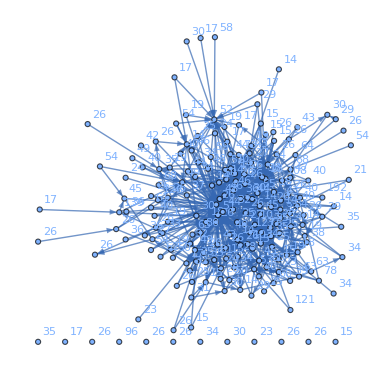

```mathematica
AdjacencyGraph[rectangularMat, VertexLabels->x_:> functional[[x+1, 2]]]
```

```mathematica
ByteCount[SparseArray[rectangularMat]]
```

5424

```mathematica
ByteCount[mutemat]*200
```

24840000

```mathematica
ByteCount[mutemat]
```

```mathematica
200*100
```

20000

```mathematica
Dimensions[mutemat]
```

{99}

```mathematica
ByteCount[SparseArray[mutemat]]
```

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in SparseArray[{{1,0,1,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«49»},«49»,«49»}].

124248

```mathematica
functional[[]]
```

### Getting peaks v2

```mathematica
functional = Select[out, #[[2]]!=-Infinity&];
```

```mathematica
outa =Association[ParallelMap[#[[1]]->#[[2]]&, out]];
```

```mathematica
funcassoc = Select[outa, #!=-Infinity&];
```

```mathematica
mutemat = Module[{digs},
ParallelTable[
digs = IntegerDigits[functional[[i, 1]],  4, 4^3];
Boole[Count[Unitize[digs - IntegerDigits[functional[[j, 1]],  4, 4^3]], 1]==1],
{i, 1, Length[functional[[;;200]]] - 1}, {j, i + 1, Length[functional[[;;200]]]}]];
```

```mathematica
maxLen=Max[Length/@mutemat];
rectangularMat=PadRight[#,maxLen]&/@mutemat;
```

```mathematica
ag=  AdjacencyGraph[rectangularMat];
```

```mathematica
Graph3D[ag,
ViewVertical->{0,0,1},EdgeShapeFunction->Function[Line[#1]],
VertexCoordinates->
MapThread[Append,{GraphEmbedding[ag],
Lookup[funcassoc,functional[[VertexList[ag] + 1, 1]]]/3}],
Axes->True]
```

-Graphics3D-

```mathematica
Graph3D[ag,
ViewVertical->{0,0,1},EdgeShapeFunction->Function[Line[#1]],
VertexCoordinates->
MapThread[Append,{GraphEmbedding[ag],
Log[Lookup[funcassoc,functional[[VertexList[ag] + 1, 1]]]]}]]
```

-Graphics3D-

```mathematica
{2*#[[1]], 2*#[[2]], #[[3]]}&/@ GraphEmbedding[]
```

{{6.87196,-6.47835,14/3},{6.93746,-6.87415,26/3},{8.70858,-5.5162,17},{8.03758,-6.2193,6},{7.67462,-7.79582,10},{8.55302,-7.5151,14/3},{7.94958,-5.70956,37/3},{6.80138,-3.29745,26/3},{6.48982,-7.12624,52/3},{7.57674,-5.32873,6},{9.56653,-6.08582,14/3},{9.33328,-5.57433,26/3},{9.91736,-8.26135,36},{8.47709,-8.57449,6},{6.71498,-5.76538,15},{7.92983,-7.20739,14/3},{6.86166,-7.13761,9},{9.02891,-6.00483,26/3},{8.80101,-4.98044,6},{9.66137,-7.29281,34/3},{9.23505,-7.54886,40/3},{5.60422,-5.64619,25/3},{11.0249,-3.12131,49/3},{8.1207,-4.56335,10},{8.92585,-7.65839,43/3},{9.13016,-7.20197,35/3},{8.59055,-5.45525,28/3},{11.5884,-8.44259,58/3},{9.6524,-5.16481,34/3},{7.65265,-7.13858,68/3},{9.21322,-8.9997,25/3},{10.1384,-6.87345,23/3},{8.29141,-8.89447,26/3},{7.78404,-7.99533,53/3},{6.48166,-9.38174,26/3},{8.22958,-8.12305,5},{7.24769,-8.49882,5},{8.41367,-6.05204,5},{9.5104,-8.36661,55/3},{9.2006,-8.53054,19/3},{7.05202,-8.86226,5},{7.18842,-9.71255,8},{5.77515,-6.13192,10},{7.51062,-5.95378,37/3},{10.1809,-7.65537,46/3},{6.97903,-5.65386,19/3},{5.37638,-3.44717,50/3},{5.31516,-1.71964,18},{7.41743,-5.12925,17/3},{7.72404,-3.50541,70/3},{5.89877,-7.94153,17/3},{0.27882,-6.6632,32/3},{5.13741,-5.09371,17/3},{5.75931,-8.67709,19/3},{3.44159,-6.25111,17/3},{2.34313,-8.35263,15},{4.615,-4.12137,26/3},{6.82779,-3.81537,26/3},{5.18412,-8.16386,8},{0.217783,-7.86446,19/3},{6.56557,-5.13984,26/3},{2.06985,-3.46763,16},{5.06225,-6.22356,26/3},{7.92261,-5.34622,26/3},{8.4973,-6.5321,26/3},{7.60581,-5.61056,14/3},{8.9019,-7.34541,26/3},{11.8277,-5.55405,35/3},{11.2712,-6.54146,7},{9.27311,-6.9688,14/3},{9.13225,-4.60332,11},{9.62059,-6.81224,26/3},{7.36307,-9.30162,34/3},{7.77074,-9.67052,50/3},{6.40778,-8.27591,14/3},{8.31926,-7.23204,26/3},{2.5291,-5.0514,103/3},{6.28874,-7.531,18},{3.24949,-6.76701,80/3},{5.77464,-4.22634,139/3},{4.48873,-7.77436,14/3},{4.61866,-7.3421,9},{3.1351,-7.39497,26/3},{4.74559,-5.1512,26/3},{9.89345,-6.52446,35/3},{9.28808,-6.32782,40/3},{8.95712,-8.06066,43/3},{9.97083,-9.17296,25/3},{6.13298,-6.89535,21},{6.12276,-8.60783,10},{6.07788,-8.17877,35/3},{8.05679,-7.96238,49/3},{8.7567,-8.8185,103/3},{10.7131,-9.32539,20},{0.217783,-11.6116,26},{7.03556,-9.2581,35/3},{8.14878,-7.51723,28/3},{8.52666,-6.84406,127/3},{9.63571,-9.33424,15},{5.98499,-7.59965,13},{9.64559,-10.4221,65/3},{6.17789,-3.91165,121/3},{3.96336,-10.7713,25/3},{6.48247,-8.63279,23/3},{5.40102,-9.51947,35/3},{6.9255,-7.96846,26/3},{5.94286,-9.95269,43/3},{5.27935,-11.176,31/3},{5.93743,-11.0761,26/3},{7.18437,-6.13598,5},{8.54068,-3.44936,46/3},{7.78626,-6.26423,5},{9.03619,-4.0954,12},{7.40346,-4.59499,5},{8.18358,-4.27971,44/3},{8.72475,-3.87114,19/3},{7.71834,-4.62078,5},{5.88691,-8.95052,73/3},{3.48846,-5.47565,32/3},{5.77125,-0.376974,8},{4.79346,-8.42987,10},{4.20546,-7.63414,62/3},{7.3697,-7.60607,12},{7.11749,-6.75324,40/3},{5.06873,-7.11991,44/3},{5.25496,-8.46852,19/3},{4.43599,-8.17792,50/3},{1.22817,-11.6116,18},{7.28505,-4.12749,17/3},{7.4979,-6.66769,17/3},{3.51585,-6.74193,32/3},{8.5614,-2.28697,12},{8.21807,-6.269,17/3},{5.74077,-3.12714,44/3},{6.29095,-0.251593,19/3},{2.23855,-11.6116,17/3},{4.44189,-6.15802,26/3},{9.90542,-3.58722,26/3},{3.48694,-7.78265,43/3},{11.9068,-4.26118,12},{5.8175,-5.23883,18},{7.18076,-3.5771,44/3},{3.24894,-11.6116,19/3},{4.25932,-11.6116,32},{7.00233,-6.26805,26/3},{11.6306,-3.71296,16},{9.01015,-3.76666,26/3},{4.4387,-6.59049,26/3},{5.26971,-11.6116,61/3},{7.25161,-5.53736,26/3},{8.92507,-6.56728,14/3},{10.2598,-7.88479,26/3},{10.8346,-6.9322,38/3},{10.0064,-6.22263,29/3},{9.27038,-6.66948,40/3},{6.66957,-4.6988,14/3},{7.97678,-6.79418,59/3},{7.20972,-5.18097,26/3},{8.19024,-9.88658,17},{7.5435,-8.83222,29/3},{8.46605,-9.16438,34/3},{10.4221,-8.978,40/3},{10.1006,-7.23864,21},{7.2263,-8.10125,14/3},{8.4139,-2.72708,26/3},{5.95269,-4.45562,29/3},{5.53769,-4.57573,46/3},{6.82529,-0.217783,40/3},{4.06286,-4.27058,58/3},{9.21591,-1.41993,14},{8.17306,-4.90928,14/3},{9.58863,-4.03837,9},{11.3419,-3.28681,26/3},{4.56964,-6.89901,29/3},{4.12573,-5.08145,40/3},{6.28009,-11.6116,40/3},{10.3133,-5.5775,34/3},{9.64079,-5.47312,40/3},{8.66197,-9.72113,47/3},{10.8397,-6.21541,25/3},{7.29048,-11.6116,64},{8.53985,-7.93277,10},{9.01765,-9.41565,34/3},{6.79997,-8.54911,20},{11.2597,-9.80538,27},{9.83548,-4.62663,34/3},{11.5453,-7.30946,64/3},{6.21152,-4.89689,35/3},{7.678,-8.43526,34/3},{4.72282,-5.74981,28/3},{3.74081,-4.74507,68/3},{4.69516,-6.3068,49/3},{5.96864,-9.37184,42},{8.30086,-11.6116,25/3},{6.08908,-5.4446,23/3},{9.31125,-11.6116,34/3},{4.86164,-7.54493,26/3},{10.3216,-11.6116,11},{11.332,-11.6116,26/3}}

```mathematica
ConvexHullMesh[{2*#[[1]], 2*#[[2]], #[[3]]}&/@ GraphEmbedding[]]
```

-Graphics3D-

```mathematica
ConvexHullMesh[{2*#[[1]], 2*#[[2]], #[[3]]}&/@ GraphEmbedding[]]
```

-Graphics3D-

### Peaks v3

```mathematica
mutemat[[1]]
```

{1,0,1,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
sa = SparseArray[rectangularMat];
```

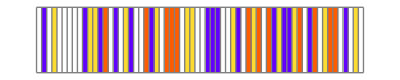

```mathematica
RuleSequencePlot[{functional[[1,1]], 4, 1}]
```

```mathematica
Flatten[sa[[1]]["ExplicitPositions"]]
```

{1,3,5,10,15,35,65,150}

```mathematica
Count[Unitize[IntegerDigits[functional[[1,1]], 4, 64] - IntegerDigits[functional[[10, 1]], 4, 64]], 1] == 1
```

False

```mathematica
Length[mutemat[[1]]]
```

199

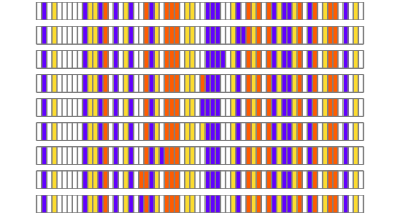

```mathematica
GraphicsColumn[Prepend[RuleSequencePlot[{functional[[# +1, 1]], 4, 1}]&/@  Flatten[sa[[1]]["ExplicitPositions"]], RuleSequencePlot[{functional[[1,1]], 4, 1}]]]
```

```mathematica
Length[mutemat]
```

199

```mathematica
Length[mutemat[[2]]]
```

198

```mathematica
Length[mutemat[[All, -1]]]
```

199

```mathematica
Length[Join[mutemat[[;;1, 2]],mutemat[[2]]]]
```

199

```mathematica
Length[mutemat[[102]]]
```

98

```mathematica
mutemat[[;;99, 100]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Dimensions[mutemat]
```

{199}

```mathematica
Grid@mutemat[[;;5, All]]
```

1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |

```mathematica
matfilled = Append[Table[Join[Part[mutemat, Sequence@@#]&/@Table[{j, i - j }, {j, i - 1}], mutemat[[i]]], {i, 199}], mutemat[[All, -1]]];
```

```mathematica
Flatten[Position[#, 1]] + 1&/@
```

{{2,4,6,11,16,36,66,151},{2,8,12,18,67,152},{5,9,13,21,68,153},{2,10,14,19,38,69,154},{4,23},{2,7,8,10,11,16,70,156},{7,8,9,17,24,43,71,157},{3,7,8,12,18,72,158},{4,8,13,25,159},{5,7,14,19,44,73,160},{2,7,12,14,16,49,75,164},{3,9,12,15,18,76,165},{4,10,27,52},{5,11,12,19,53,166},{13},{2,7,12,17,18,19,57,81,171},{8,17,18,20,32,58,61,82,172},{3,9,13,17,18,62,83,173},{5,11,15,17,20,174},{18,20,33,59,64,84,175},{4,23,25,27,86,178},{30,34,40,88,180},{6,22,35},{8,25,26,32,43,90,182},{10,22,25,27,92,184},{25,27,29,32,50,188},{14,22,26,27,28,29,52,97,190},{28,98,191},{27,28,30,33,100},{23,30,31,34,54,193},{31,56,103,194},{18,25,27,33,35,58,61,104,195},{21,30,33,34,35,59,64,106,197},{23,31,34,60,108,198},{24,33,34,65,109,199},{2,37,38,41,49,57,110,200},{37,38,41,51,112},{5,37,38,39,40,41,44,53,114},{39,40,45,59},{23,39,40,42,46,54,60,116},{37,38,39,42,47,55,117},{41,42,48,56,120},{8,25,45,50,58,121},{11,39,45,46,47,53,124},{40,44,45,46,59},{41,45,46,48,54,60,126},{42,45,48,55,127},{43,47,48,56,128},{12,37,50,51,53,55,57,129},{27,44,50,52,58},{38,50,52,53,55,130},{14,28,51,52,131},{15,39,45,50,52,54,55,133},{31,41,47,54,56,60,135},{42,48,50,52,54,56,136},{32,43,49,55,56},{17,37,50,58,137},{18,33,44,51,58,59,61,138},{21,34,40,46,59,60,64,141},{35,41,47,55,60,143},{18,33,59,62,63,64,65,145},{19,62,146},{62,64,65,147},{21,34,60,62,64,65,148},{36,62,64,65,150},{2,67,69,70,75,81,110,151},{3,67,72,76,83,85,152},{4,86,153},{5,67,73,114,154},{7,67,71,72,73,75,81,156},{8,71,72,82,90,121,157},{9,68,71,72,74,76,83,91,158},{11,70,71,74,124,160},{73,74,79,125,162},{12,67,71,76,81,129,164},{13,68,73,76,79,83,96,165},{99,132},{79,80,84,100,167},{75,77,79,101,134,168},{79,102,169},{17,67,71,76,82,83,137,171},{18,72,82,83,84,104,138,145,172},{19,68,73,77,82,83,105,146,173},{21,79,83,106,141,148,175},{68,89,91,96,105,177},{22,69,87,92,97,178},{87,88,99,113,179},{23,88,94,108,116,180},{86,95,119,181},{25,72,91,92,104,121,182},{73,86,91,93,95,96,105,183},{26,87,91,93,97,122,184},{92,93,95,98,185},{89,108,126,187},{90,92,94},{77,86,92,98,101,105,189},{28,87,93,98,99,100,102,131,190},{29,94,97,98,99,101,144,191},{78,88,98,99,103,132,192},{30,79,98,101,102,106},{80,97,99,101,107,134},{81,98,101,103,109},{32,100,103,194},{33,83,91,105,106,109,138,145,195},{84,86,92,97,105,107,146,196},{34,85,101,105,107,108,109,141,148,197},{102,106,107,108,142,149},{35,89,95,107,108,143,198},{36,103,105,107,150,199},{37,67,111,112,114,117,129,137,200},{111,118,121,138},{38,111,113,114,117,130,139},{88,113,116,120,123,132,140},{39,70,111,113,115,116,117,124,133},{115,116,119,125,134,142},{41,89,114,115,116,120,126,135,143},{42,111,113,115,118,119,120,127,136},{112,118,119,120},{90,116,118,119,120},{43,114,117,118,119,120,128},{44,72,91,112,122,138},{93,122,123,131},{114,123,126,128,132,140},{45,74,115,125,126,127,133},{75,116,125,126,134,142},{47,95,117,124,125,126,128,135,143},{48,118,125,128,136},{49,121,124,127,128},{50,76,111,130,133,136,137},{52,113,130,131,132,133,136,139},{53,98,123,131,132},{78,100,114,124,131,132,135,140},{54,115,125,130,131,134,135,136},{80,102,116,126,134,135,142},{55,117,127,133,134,135,143},{56,118,128,130,131,134},{58,82,111,130,138,139},{59,83,105,112,122,138,141,145},{113,131,138,140},{114,124,133,140,143},{60,85,107,139,142,143,148},{108,116,126,135,142,143,149},{61,109,117,127,136,141,142,143},{99},{62,83,105,139,146,147,148,150},{63,84,106,146,149},{64,146,148,150},{65,85,107,142,146,148,149,150},{108,143,147,149},{66,110,146,148,149},{2,67,152,154,156,164,171,200},{3,68,152,155,158,165,173,177},{4,69,159,178},{5,70,152,155,160,166,174},{153,155,162,168,176},{7,71,152,157,158,160,164,171},{8,72,157,158,159,161,172,182},{9,73,153,157,158,162,165,173,183},{10,154,158,161,184},{11,74,155,157,161,162,166,174},{158,160,161,162,167,175,186},{75,156,159,161,162,168,176},{170},{12,76,152,157,165,166,171},{13,77,153,159,165,168,173,189},{15,155,161,165,167,168,174},{79,162,167,168,169,175},{80,156,163,166,167,168,176},{81,168,170},{164,170,194},{17,82,152,157,165,172,173,174},{18,83,158,172,173,175,195},{19,84,153,159,166,172,173,176,196},{20,155,161,167,172,175,176},{21,85,162,168,173,175,176,197},{156,163,169,174,175,176},{86,153,181,183,189,196},{22,87,154,179,184,190},{88,179,180,192},{23,89,180,187,193,198},{90,178},{25,91,158,183,184,186,188,195},{92,159,178,183,185,189,196},{26,93,160,179,183,185,186,190},{94,184,185,191},{162,183,185,187,197},{95,181,187,193,198},{27,183,189,190,195},{97,166,178,184,189,191,196},{28,98,179,185,189,191,192},{29,99,186,190,191,192},{100,180,191,192,193,194},{31,181,188,193,194,198},{32,104,171,193,194},{33,105,173,183,189,196,197,199},{106,174,178,184,190,196},{34,107,176,187,196,198,199},{35,109,181,188,194,198},{36,110,196,198},{37,111,152}}

```mathematica
Select[Range[Length[]],Max[functional[[Flatten[Position[matfilled[[#]], 1]] + 1, 2]]]<functional[[#, 2]]&]
```

{13,23,77,80,95,139,141,144,163,169,181,188}

```mathematica
Length[]
```

12

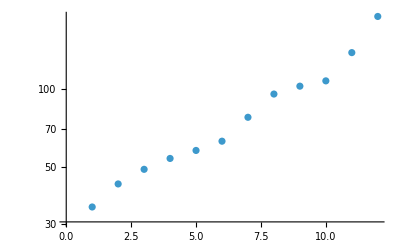

```mathematica
ListPlot[Sort[functional[[#, 2]]&/@ ], ScalingFunctions->"Log"]
```

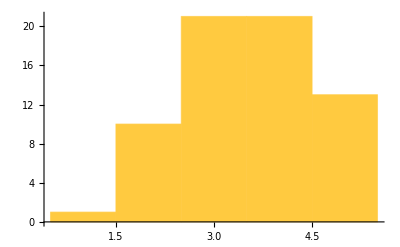

```mathematica
Histogram[Flatten[Module[{digs}, Table[
digs = IntegerDigits[functional[[[[i]], 1]],  4, 4^3];
Count[Unitize[digs - IntegerDigits[functional[[[[j]], 1]],  4, 4^3]], 1],
{i, Length[] - 1}, {j, i + 1, Length[]}]]]]
```

```mathematica
TJoin[mutemat[[;;1, 2]],mutemat[[2]]]
```

```mathematica
peaks = Select[Range[Length[mutemat]]]
```

```mathematica
Length/@mutemat
```

{199,198,197,196,195,194,193,192,191,190,189,188,187,186,185,184,183,182,181,180,179,178,177,176,175,174,173,172,171,170,169,168,167,166,165,164,163,162,161,160,159,158,157,156,155,154,153,152,151,150,149,148,147,146,145,144,143,142,141,140,139,138,137,136,135,134,133,132,131,130,129,128,127,126,125,124,123,122,121,120,119,118,117,116,115,114,113,112,111,110,109,108,107,106,105,104,103,102,101,100,99,98,97,96,95,94,93,92,91,90,89,88,87,86,85,84,83,82,81,80,79,78,77,76,75,74,73,72,71,70,69,68,67,66,65,64,63,62,61,60,59,58,57,56,55,54,53,52,51,50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}